# Figure 1

Clicking Run all evaluates the whole notebook from top to bottom . Some computations may take a while, so please wait until all cells have finished running .

```mathematica
Button["Run all",
With[{nb=ButtonNotebook[]},
FrontEndTokenExecute[nb,"EvaluateNotebook"];
SelectionMove[nb,After,Notebook]
]
]
```

Run all

```mathematica
ClearAll["Global`*"];
```

```mathematica
SeedRandom[1234];
Lns=ConstantArray[{5,5},3]//Flatten;
ns=Table[i,{i,3,6,1}];
σnls=Table[Table[RandomInteger[{1,400},Lns[[i]]]/100,{i,ns[[k]]}],{k,Length[ns]}];
samples=4*10^6;
Rs=Table[(∑_(i=1)^ns[[k]] (∏_(j=1)^Lns[[i]] RandomVariate[RayleighDistribution[σnls[[k,i,j]]],samples])),{k,1,Length[ns],1}];
mcPDF=Table[Rs[[k]]/√Moment[Rs[[k]],2],{k,1,Length[ns]}];
σSS=ConstantArray[σnls[[1,2]],6];
RsS=Table[(∑_(i=1)^ns[[k]] (∏_(j=1)^Lns[[i]] RandomVariate[RayleighDistribution[σSS[[i,j]]],samples])),{k,1,Length[ns],1}];
mcPDFS=Table[RsS[[k]]/√Moment[RsS[[k]],2],{k,1,Length[ns]}];
```

```mathematica
SeedRandom[3];
approx=Table[0,{Length[ns]}];Gs=approx;
mus=Table[0,{Length[ns]}];
sigmas=Table[0,{Length[ns]}];
For[j=1,j<=Length[ns],j++,
σs=σnls[[j]];
N1=Length[σs];
mus[[j]]=∑_(k=1)^N1 (√(π/2))^Length[σs[[k]]](∏_(l=1)^Length[σs[[k]]] σs[[k,l]]);(*mean*)
sigmas[[j]]=(∑_(k=1)^N1 ((∏_(l=1)^Length[σs[[k]]] (((4-π)/2)σs[[k,l]]^2+(√(π/2)σs[[k,l]])^2))-∏_(l=1)^Length[σs[[k]]] (√(π/2)σs[[k,l]])^2))^(1/2);(*standar deviation*)
Gs[[j]]=RandomVariate[NormalDistribution[mus[[j]],sigmas[[j]]],samples];
approx[[j]]=Gs[[j]]/√Moment[Gs[[j]],2];
];
SeedRandom[3];
approxS=Table[0,{Length[ns]}];
For[j=1,j<=Length[ns],j++,
σs=σSS[[;;ns[[j]]]];
N1=Length[σs];
mus=∑_(k=1)^N1 (√(π/2))^Length[σs[[k]]](∏_(l=1)^Length[σs[[k]]] σs[[k,l]]);(*mean*)
sigmas=(∑_(k=1)^N1 ((∏_(l=1)^Length[σs[[k]]] (((4-π)/2)σs[[k,l]]^2+(√(π/2)σs[[k,l]])^2))-∏_(l=1)^Length[σs[[k]]] (√(π/2)σs[[k,l]])^2))^(1/2);(*standar deviation*)
GsS=RandomVariate[NormalDistribution[mus,sigmas],samples];
approxS[[j]]=GsS/√Moment[GsS,2];
];
```

```mathematica
aPb=Table[0,{j,ns}];
Pb=Table[0,{j,ns}];
Subscript[N, 0]= RandomVariate[NormalDistribution[0,√(1/2)],samples];
a=1;b=2;
snr=Table[10^(l/10),{l,-20,60,2}];
Timing[
pr=Table[0,{Length[snr]}];
For[i=1,i<=Length[ns],i++,
H1=mcPDF[[i]];
For[j=1,j≤Length[snr],j++,
ρ1=snr[[j]] H1^2;
cont=0;
cont=Total[UnitStep[Subscript[N, 0]-a √((b ρ1)/2)]];
pr[[j]]={N[10Log10[snr[[j]]]],N[cont/samples,300]};
];
Pb[[i]]=pr;
];
]
```

{6.45313,Null}

```mathematica
a=1;b=2;
snr=Table[10^(l/10),{l,-20,60,2}];
Subscript[N, 0]= RandomVariate[NormalDistribution[0,√(1/2)],samples];
Timing[
pr=Table[0,{Length[snr]}];
For[i=1,i<=Length[ns],i++,
H1=approx[[i]];
For[j=1,j≤Length[snr],j++,
ρ1=snr[[j]] H1^2;
cont=0;
cont=Total[UnitStep[Subscript[N, 0]-a √((b ρ1)/2)]];
pr[[j]]={N[10Log10[snr[[j]]]],N[cont/samples,200]};
];
aPb[[i]]=pr;
];
]
```

{6.09375,Null}

```mathematica
PbS=Table[0,{j,ns}];
a=1;b=2;
Subscript[N, 0]= RandomVariate[NormalDistribution[0,√(1/2)],samples];
snr=Table[10^(l/10),{l,-20,60,2}];
Timing[
pr=Table[0,{Length[snr]}];
For[i=1,i<=Length[ns],i++,
H1=mcPDFS[[i]];
For[j=1,j≤Length[snr],j++,
ρ1=snr[[j]] H1^2;
cont=0;
cont=Total[UnitStep[Subscript[N, 0]-a √((b ρ1)/2)]];
pr[[j]]={N[10Log10[snr[[j]]]],N[cont/samples,200]};
];
PbS[[i]]=pr;
];
]
```

{6.3125,Null}

```mathematica
a=1;b=2;
aPbS=Table[0,{j,ns}];
snr=Table[10^(l/10),{l,-20,60,2}];
Subscript[N, 0]= RandomVariate[NormalDistribution[0,√(1/2)],samples];
Timing[
pr=Table[0,{Length[snr]}];
For[i=1,i<=Length[ns],i++,
H1=approxS[[i]];
For[j=1,j≤Length[snr],j++,
ρ1=snr[[j]] H1^2;
cont=0;
cont=Total[UnitStep[Subscript[N, 0]-a √((b ρ1)/2)]];
pr[[j]]={N[10Log10[snr[[j]]]],N[cont/samples,200]};
];
aPbS[[i]]=pr;
];
]
```

{5.89063,Null}

```mathematica
Table[Subscript[EH, j]=∑_(m=1)^ns[[j]] (∏_(i=1)^Lns[[m]] 2 σnls[[j,m,i]]^2)+2∑_(m=1)^ns[[j]] ∑_(k=m+1)^ns[[j]] (∏_(i=1)^Lns[[m]] √(π/2)σnls[[j,m,i]])(∏_(i=1)^Lns[[m]] √(π/2)σnls[[j,k,i]]^2),{j,Length[ns]}];
Table[Subscript[EHS, j]=∑_(m=1)^ns[[j]] (∏_(i=1)^Lns[[m]] 2 σSS[[m,i]]^2)+2∑_(m=1)^ns[[j]] ∑_(k=m+1)^ns[[j]] (∏_(i=1)^Lns[[m]] √(π/2)σSS[[m,i]])(∏_(i=1)^Lns[[m]] √(π/2)σSS[[k,i]]^2),{j,Length[ns]}];
```

```mathematica
Table[Subscript[L, n]=Lns[[n]],{n,Length[Lns]}];a=1;b=2;
terms=300;
Paber[M_,ρ_,δ_,σs_,EH_]:=(a Gamma[1/2+M])/(2 √π Gamma[2M+1])((2EH)/(ρ b))^M(∏_(n=1)^M 1/2^(Subscript[L, n]-1)(∏_(i=1)^Subscript[L, n] 1/σs[[n,i]]^2)∏_(i=2)^Subscript[L, n] N[Gamma[(i-1)δ],terms]);
δ1=10^-0.8;
δ1s=10^-0.95;
pts=Table[Table[{r,Paber[ns[[i]],10^(r/10),δ1,σnls[[i]],Subscript[EH, i]]},{r,-20,60,2}],{i,Length[ns]}];
ptsS=Table[Table[{r,Paber[ns[[i]],10^(r/10),δ1s,σSS[[;;ns[[i]]]],Subscript[EHS, i]]},{r,-20,60,2}],{i,Length[ns]}];
```

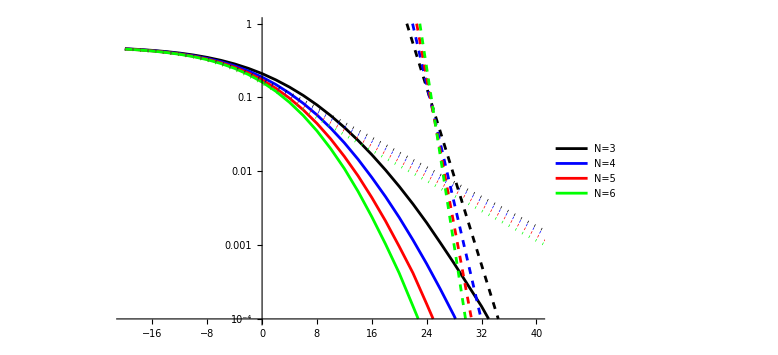

```mathematica
ListLogPlot[{PbS[[1]],PbS[[2]],PbS[[3]],PbS[[4]],aPbS[[1]],aPbS[[2]],aPbS[[3]],aPbS[[4]],ptsS[[1]],ptsS[[2]],ptsS[[3]],ptsS[[4]]},PlotStyle->{Black,Blue,Red,Green,{Black,Dotted},{Blue,Dotted},{Red,Dotted},{Green,Dotted},{Black,Dashed},{Blue,Dashed},{Red,Dashed},{Green,Dashed}},Joined->True,PlotRange->{{-20,40},{10^-4,1}},PlotLegends->{"N=3","N=4","N=5","N=6"},ImageSize->Large]
```

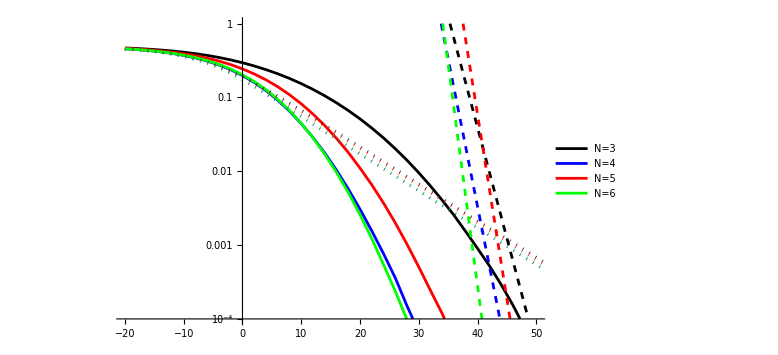

```mathematica
ListLogPlot[{Pb[[1]],Pb[[2]],Pb[[3]],Pb[[4]],aPb[[1]],aPb[[2]],aPb[[3]],aPb[[4]],pts[[1]],pts[[2]],pts[[3]],pts[[4]]},PlotStyle->{Black,Blue,Red,Green,{Black,Dotted},{Blue,Dotted},{Red,Dotted},{Green,Dotted},{Black,Dashed},{Blue,Dashed},{Red,Dashed},{Green,Dashed}},Joined->True,PlotRange->{{-20,50},{10^-4,1}},PlotLegends->{"N=3","N=4","N=5","N=6"},ImageSize->Large]
```